SVD Example with Morse Potential (Scattering Calculation)
1. Set up Morse potential:

```mathematica
Vmorse[a_,re_,De_,r_]:=De (1-ⅇ^(-(r-re)/a))^2-De
Nchan=3;
Eth={0.0,3.0,5.0};
α=1;
re=1;
l=0;
rmin=0.0;
rmax=10.0;
D11=1.0;
D22=4.0;
D33=6.0;
V12=0.2;
V23=0.2;
r12=0.5;
r23=1.0;
a12=0.5;
a23=0.5;
no =1;

Vdiag[r_,a_,re_,D11_,D22_,D33_,Eth_]:=({{Vmorse[a,re,D11,r]+Eth[[1]], 0, 0}, {0, Vmorse[a,re,D22,r]+Eth[[2]], 0}, {0, 0, Vmorse[a,re,D33,r]+Eth[[3]]}});
Vcoupling[r_,a_,V12_,V23_,r12_,r23_,a12_,a23_]:=({{0, V12 ⅇ^(-(r-r12)^2/a12^2), 0}, {V12 ⅇ^(-(r-r12)^2/a12^2), 0, V23 ⅇ^(-(r-r23)^2/a23^2)}, {0, V23 ⅇ^(-(r-r23)^2/a23^2), 0}});

Vmat[r_,a_,re_,D11_,D22_,D33_,V12_,V23_,r12_,r23_,a12_,a23_,Eth_]:=Vdiag[r,a,re,D11,D22,D33,Eth]+Vcoupling[r,a,V12,V23,r12,r23,a12,a23]
```

```mathematica
VV[r_]=Vmat[r,α,re,D11,D22,D33,V12,V23,r12,r23,a12,a23,Eth];
```

3. Calculate the weights, abscissa for the range 0,1. Then to re-scale them to an arbitrary range x∈[a,b] we multiply the abscissa by x_i→a+x_i (b-a)

```mathematica
M=80;precision=20;{xnodes,wn,errwn}=NIntegrate`LobattoRuleData[M+2,precision];
a=rmin;b=rmax;xn=xnodes(b-a)+a;
m = 3*(M+1)
```

243

2. Define DVR basis functions

```mathematica
χGL[nodes_,i_,x_]:=Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,1,i-1}]Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,i+1,M+2}];
```

4. Construct matrices with basis functions and their derivatives.

```mathematica
πfuns=Table[wn[[i]]^(-1/2)χGL[xn,i,xn[[j]]],{i,1,M+2},{j,1,M+2}];
πfunsp=Table[wn[[i]]^(-1/2)D[χGL[xn,i,x],x]/.x->xn[[j]],{i,1,M+2},{j,1,M+2}];
```

5. Construct table for the potential where each element is the potential matrix evaluated at each element of x_n.

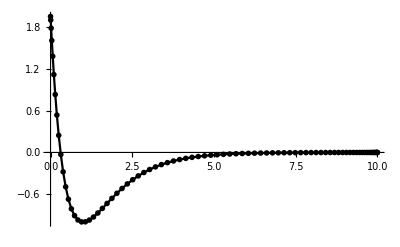

```mathematica
ListPlot[Transpose[{xn,VV[xn][[1,1]]}],Joined->True,PlotRange->All]
```

```mathematica
VVTable = Table[VV[xn[[i]]],{i,1,M+2}];
```

```mathematica
Dimensions[VVTable]
```

{82,3,3}

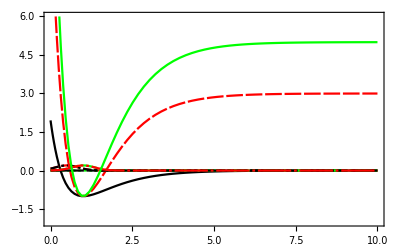

```mathematica
ListPlot[Flatten[Table[Transpose[{xn,VVTable[[;;,i,j]]}],{i,1,3},{j,1,3}],1],Joined->True,PlotStyle->{Black,Red,Green},PlotMarkers->None,Frame->True,PlotRange->{-2,6}]
```

6. Find eigenvalues and eigenvectors of the potential matrix at each element of x_n.

```mathematica
ValsVecs = Table[Sort[Transpose[Eigensystem[VVTable[[i]]]]],{i,1,M+2}];
```

```mathematica
AdiabaticUV=Table[{{xn[[iR]],ValsVecs[[iR,n,1]]},ValsVecs[[iR,n,2]]},{iR,1,M+2},{n,1,3}];
```

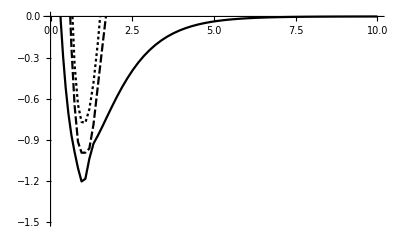

```mathematica
ListPlot[Table[AdiabaticUV[[1;;M+2,n,1]],{n,1,3}],Joined->True,PlotMarkers->None,PlotRange->{-1.5,0}]
```

Fix any phase discrepancies between neighboring R points.  Check if the overlap between neighboring eigenstates is less than zero:

```mathematica
Table[AdiabaticUV[[iR,n,2]].AdiabaticUV[[iR+1,n,2]],{iR,1,M+1},{n,1,3}]
```

{{1.,1.,1.},{1.,1.,1.},{0.999999,0.999999,1.},{0.999997,0.999997,1.},{0.999994,0.999994,1.},{0.999986,0.999986,0.999999},{0.999969,0.999967,0.999998},{0.99993,0.999923,0.999993},{0.99984,0.999813,0.999974},{0.99963,0.999518,0.999888},{0.999139,0.998616,0.999477},{0.997937,0.995234,0.997297},{0.994581,0.980354,0.985772},{-0.980195,0.939057,0.958803},{0.897837,0.874909,0.975814},{0.927072,0.926892,0.998467},{-0.994833,0.989264,0.99443},{-0.99045,0.98323,0.990063},{-0.403462,0.392096,0.984576},{0.997264,0.969417,0.97215},{0.999931,0.984504,0.984572},{0.999997,0.99664,0.996643},{1.,0.99952,0.999521},{1.,0.99995,0.99995},{1.,0.999996,0.999996},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}}

Create a temporary array

```mathematica
UV=AdiabaticUV;
```

Flip the phase if the overlap is less than zero.

```mathematica
Do[
Block[{check},
Do[
check=UV[[iR,n,2]].UV[[iR+1,n,2]];
UV[[iR+1,n,2]]=If[check<0,-UV[[iR+1,n,2]],UV[[iR+1,n,2]]],
{n,1,3}
]
]
,{iR,1,M+1}
]
```

Check if it worked:

```mathematica
Table[Table[UV[[iR,n,2]].UV[[iR+1,n,2]],{n,1,3}],{iR,1,M+1}]
```

{{1.,1.,1.},{1.,1.,1.},{0.999999,0.999999,1.},{0.999997,0.999997,1.},{0.999994,0.999994,1.},{0.999986,0.999986,0.999999},{0.999969,0.999967,0.999998},{0.99993,0.999923,0.999993},{0.99984,0.999813,0.999974},{0.99963,0.999518,0.999888},{0.999139,0.998616,0.999477},{0.997937,0.995234,0.997297},{0.994581,0.980354,0.985772},{0.980195,0.939057,0.958803},{0.897837,0.874909,0.975814},{0.927072,0.926892,0.998467},{0.994833,0.989264,0.99443},{0.99045,0.98323,0.990063},{0.403462,0.392096,0.984576},{0.997264,0.969417,0.97215},{0.999931,0.984504,0.984572},{0.999997,0.99664,0.996643},{1.,0.99952,0.999521},{1.,0.99995,0.99995},{1.,0.999996,0.999996},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.}}

7. Construct T matrix.

```mathematica
W=DiagonalMatrix[wn];
T=Table[πfunsp[[i]].W.πfunsp[[j]],{i,2,M+2},{j,2,M+2}];
```

```mathematica
Dimensions[T]
```

{81,81}

8. Construct O matrix.

i. Create a collective index:

```mathematica
NumR = M+1; NumAng=3;
iμ=Flatten[Table[Table[{iR,mu},{iR,1,M+1}],{mu,1,NumAng}],1];
indexpos[iR_,mu_]:=Position[iμ,{iR,mu}][[1,1]]
ProbSize=Length[iμ]
```

243

ii. Calculate O Matrix

```mathematica
OMatrix = Table[UV[[iμ[[imu]][[1]],iμ[[imu]][[2]],2]].UV[[iμ[[jnu]][[1]],iμ[[jnu]][[2]],2]],{imu,1,ProbSize},{jnu,1,ProbSize}];
```

```mathematica
Dimensions[OMatrix]
```

{243,243}

```mathematica
MatrixForm[OMatrix[[10;;20,10;;20]]]
```

(1. | 0.99963 | 0.997642 | 0.991186 | 0.972221 | 0.909366 | 0.654709 | 0.347289 | 0.25208 | 0.369079 | 0.999272
0.99963 | 1. | 0.999139 | 0.994417 | 0.97818 | 0.919894 | 0.671896 | 0.366345 | 0.271428 | 0.3887 | 0.999557
0.997642 | 0.999139 | 1. | 0.997937 | 0.985907 | 0.93477 | 0.697589 | 0.395554 | 0.301256 | 0.418699 | 0.9986
0.991186 | 0.994417 | 0.997937 | 1. | 0.994581 | 0.954963 | 0.736306 | 0.441508 | 0.348609 | 0.465656 | 0.99384
0.972221 | 0.97818 | 0.985907 | 0.994581 | 1. | 0.980195 | 0.796652 | 0.518806 | 0.429399 | 0.54383 | 0.977934
0.909366 | 0.919894 | 0.93477 | 0.954963 | 0.980195 | 1. | 0.897837 | 0.669157 | 0.590332 | 0.692982 | 0.92175
0.654709 | 0.671896 | 0.697589 | 0.736306 | 0.796652 | 0.897837 | 1. | 0.927072 | 0.884566 | 0.939535 | 0.681526
0.347289 | 0.366345 | 0.395554 | 0.441508 | 0.518806 | 0.669157 | 0.927072 | 1. | 0.994833 | 0.998807 | 0.382313
0.25208 | 0.271428 | 0.301256 | 0.348609 | 0.429399 | 0.590332 | 0.884566 | 0.994833 | 1. | 0.99045 | 0.288418
0.369079 | 0.3887 | 0.418699 | 0.465656 | 0.54383 | 0.692982 | 0.939535 | 0.998807 | 0.99045 | 1. | 0.403462
0.999272 | 0.999557 | 0.9986 | 0.99384 | 0.977934 | 0.92175 | 0.681526 | 0.382313 | 0.288418 | 0.403462 | 1.)

9. Construct H-tilde matrix.

```mathematica
Htilde = Table[T[[iμ[[imu]][[1]],iμ[[jnu]][[1]]]]*OMatrix[[imu,jnu]]+UV[[iμ[[imu]][[1]],iμ[[imu]][[2]],1,2]]*KroneckerDelta[imu,jnu],{imu,1,ProbSize},{jnu,1,ProbSize}];

Dimensions[Htilde]
```

{243,243}

10. Find eigenvalues and eigenvectors of H̃

```mathematica
HValsVecs=Sort[Transpose[Eigensystem[Htilde]]];
```

Go through and make the eigenvectors a list of pairs so we can plot them.

11. Now we need to construct u_ν^(n)(r) given by u_ν^(n)(r) = ∑_j x_(jν,n)π_j(r), where x_(jν,n) are the elements of the eigenvector OverVector[x_n] of H̃ and π_j(r) is the j^th basis function. (For the n^th eigenvector, there are three corresponding functions u_v(r). )  The π_j(r_i)=δ_ij property then collapses the sum so that if we evaluate u_ν^(n)(r) at one of the nodes r_i then we simply get the eigenvector element x_iν^(n)

```mathematica
ufun[n_,ν_]:=Table[{xn[[j]],HValsVecs[[n,2,indexpos[j-1,ν]]] πfuns[[j,j]]},{j,2,M+2}]
```

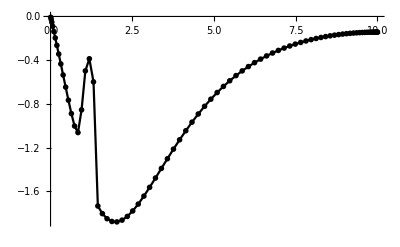

```mathematica
ListPlot[ufun[1,1],PlotRange->All,Joined->True]
```

Checking that u(r)'s go to zero at a_1

12. Construct R_11, R_12, R_21, and R_22 matrices

```mathematica
(*R11[ϵ_]:=Table[Sum[(uTable[rmin][[n,ν]]*uTable[rmin][[n,μ]])/(vals[[n]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];*)
```

```mathematica
(*R12[ϵ_]:=Table[Sum[(uTable[rmin][[n,ν]]*uTable[rmax][[n,μ]])/(vals[[n]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];*)
```

```mathematica
(*R21[ϵ_]:=Table[Sum[(uTable[rmax][[n,ν]]*uTable[rmin][[n,μ]])/(vals[[n]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];*)
```

```mathematica
(*R22[ϵ_]:=Table[Sum[(uTable[rmax][[n,ν]]*uTable[rmax][[n,μ]])/(vals[[n]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];*)
```

```mathematica
R11[ϵ_]:=Table[Sum[(ufun[n,ν][[1,2]]*ufun[n,μ][[1,2]])/(HValsVecs[[n,1]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];
R12[ϵ_]:=Table[Sum[(ufun[n,ν][[1,2]]*ufun[n,μ][[M+1,2]])/(HValsVecs[[n,1]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];
R21[ϵ_]:=Table[Sum[(ufun[n,ν][[M+1,2]]*ufun[n,μ][[1,2]])/(HValsVecs[[n,1]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];
R22[ϵ_]:=1/rmax Table[Sum[(ufun[n,ν][[M+1,2]]*ufun[n,μ][[M+1,2]])/(HValsVecs[[n,1]]-ϵ),{n,1,m}],{ν,1,3},{μ,1,3}];
```

13. Construct R(a_2)

```mathematica
RMatrix[ϵ_]:= R22[ϵ];
```

For an our current problem, R = R_22 because R_21=R_11=R_12=R(a_1) = 0.

```mathematica
RMatrix[0.1]
```

{{-4.52024,-6.44123×10^-7,1.30082×10^-9},{-6.44123×10^-7,0.587372,-9.60939×10^-15},{1.30082×10^-9,-9.60939×10^-15,0.451848}}

```mathematica
EMatrix[ϵ_]:=DiagonalMatrix[Table[(HValsVecs[[n,1]]-ϵ),{n,1,m}]]
```

```mathematica
uTable2=Table[ufun[n,μ][[M+1,2]],{n,1,ProbSize},{μ,1,NumAng}];
```

```mathematica
RTest[ϵ_]:= 1/rmax Transpose[uTable2].Inverse[EMatrix[ϵ]].uTable2;
```

```mathematica
Dimensions[RTest[ϵ]]
```

{3,3}

```mathematica
RMatrix[0]
```

{{6.5457,2.74653×10^-7,-5.47922×10^-10},{2.74653×10^-7,0.577494,4.01516×10^-15},{-5.47922×10^-10,4.01516×10^-15,0.447304}}

```mathematica
RTest[0.1]
```

{{-4.52024,-6.44123×10^-7,1.30082×10^-9},{-6.44123×10^-7,0.587372,-9.61016×10^-15},{1.30082×10^-9,-9.60932×10^-15,0.451848}}

14. Construct K matrix

i. Define the energy-normalized asymptotic solutions and their derivatives

```mathematica
f[l_,k_,r_]:=√(k/π)r SphericalBesselJ[l,k r];
g[l_,k_,r_]:=√(k/π)r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=Simplify[D[f[l,k,rp],rp]]/.rp->r; 
dgdr[l_,k_,r_]:=Simplify[D[g[l,k,rp],rp]]/. rp->r;
```

ii. Setup matrices with these solutions and their derivatives

```mathematica
F[Ε_,r_]:=DiagonalMatrix[Table[f[0,√(Ε-Eth[[ii]]),r],{ii,1,3}]];
G[Ε_,r_]:=DiagonalMatrix[Table[g[0,√(Ε-Eth[[ii]]),r],{ii,1,3}]];
dF[Ε_,r_]:=DiagonalMatrix[Table[dfdr[0,√(Ε-Eth[[ii]]),r],{ii,1,3}]];
dG[Ε_,r_]:=DiagonalMatrix[Table[dgdr[0,√(Ε-Eth[[ii]]),r],{ii,1,3}]];
```

```mathematica
KMatrix[ϵ_]:= (F[ϵ,rmax]-dF[ϵ,rmax].RTest[ϵ]).Inverse[(G[ϵ,rmax]-dG[ϵ,rmax].RTest[ϵ])];
```

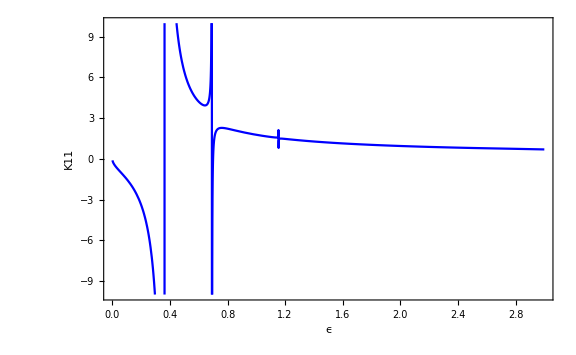

```mathematica
pk11=Plot[KMatrix[ϵ][[1,1]],{ϵ,0.001,3},Frame->True, FrameLabel->{"ϵ","K11"},ImageSize->Large,LabelStyle->Large, PlotRange->{-10,10},PlotStyle->{Blue}]
```

```mathematica
De=1;a=1;re=1;
l=0;δ[De_,Ε_]:=Arg[Hypergeometric1F1[1/2+ⅈ √Ε-√(a^2 De),1+2ⅈ √Ε,2 ⅇ^(re/a)√(a^2 De)]]
```

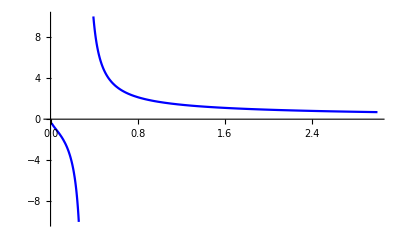

```mathematica
pbackground=Plot[Tan[δ[De,Ε]],{Ε,0.01,3.0},PlotRange->{-10,10},PlotStyle->Blue]
```

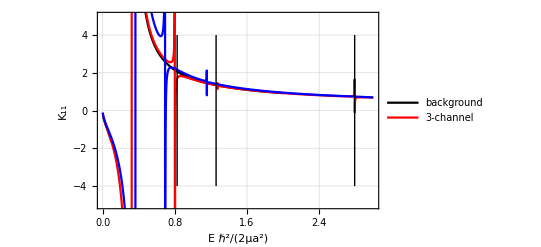

```mathematica
Show[{KK11Mathematica,pk11}]
```

## Single-channel R-matrix calculation and comparison to Numerov Method

Okay, let’s say we have just a single-channel schrodinger equation in a single partial wave of the form:

-ℏ^2/(2μ) (∂^2 ψ(r))/(∂r^2)+(V(r)+(ℏ^2 l(l+1))/(2μ r^2))ψ(r)=E ψ(r)

Multiply through by 2μ/ℏ^2

- (∂^2 ψ(r))/(∂r^2)+((2μ)/ℏ^2 V(r)+(l(l+1))/r^2)ψ(r)=k^2 ψ(r)

We choose V(r) to be the Morse potential for convenience, and we let ℏ=1,μ=1/2 so that the full effective potential in partial wave l is:

```mathematica
VEff[l_,a_,re_,De_,r_]:=De (1-ⅇ^(-(r-re)/a))^2-De+(l(l+1))/r^2
```

```mathematica
CalcCotanDelta[De_?NumberQ,ksqr_?NumberQ,rmax_?NumberQ]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,re,a},
r1=0.95 rmax;
r2=0.99rmax;
re=1;
a=1;
l=0;
k=√ksqr;
sol=NDSolve[{-u''[r]+VEff[l,a,re,De,r]u[r]==ksqr u[r],u[0]==0,u'[0]==1},u,{r,0,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]
```

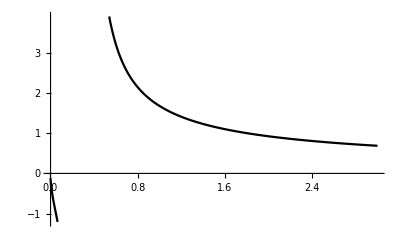

```mathematica
Plot[CalcCotanDelta[1,Ε,10]^-1,{Ε,0.001,3.0}]
```

Okay so this seems to agree with the analytical answer. Let’s try this with the R-matrix and DVR solutions.

In the current DVR scheme, we express the (reduced) radial wavefunction ψ(R) as

ψ(R)=∑_i c_i π_i(R)

Taking the log-derivative of both sides leads to:

∑_i c_i π_i(R)((ψ'(R))/(ψ(R)))^(⏞^((ℛ(R))^-1))=∑_i c_i(∂π_i(R))/(∂R)

∑_i c_i π_i(R)=((ψ'(R))/(ψ(R)))^-1∑_j c_j(∂π_i(R))/(∂R)

We wish to calculate matrix elements of the form:

π_iHπ_j=π_i-ℏ^2/(2μ)∂^2/(∂R^2)+V_eff(R)π_j=-ℏ^2/(2μ)∫_a^b ⅆR π_i(∂^2 π_j)/(∂R^2)+∫_a^b ⅆR π_i V_eff(R)π_j

Integrating the first term by parts, and using the DVR property for the second term,

π_iHπ_j=+ℏ^2/(2μ)∫_a^b ⅆR (∂π_i)/(∂R)(∂π_j)/(∂R)+V_eff(R_i)δ_ij-(ℏ^2/(2μ)[π_i(∂π_j)/(∂R)])_a^b

Call the first two terms H̃

(H̃)_ij=ℏ^2/(2μ)∫_a^b ⅆR (∂π_i)/(∂R)(∂π_j)/(∂R)+V_eff(R_i)δ_ij

The full Schrodinger equation (inside the volume) then reads

(H̃-E)c=L c

L_ij=(ℏ^2/(2μ)[π_i(∂π_j)/(∂R)])_a^b

H̃ is a hermitian matrix.  Let’s say we have its eigenvectors and bring it to diagonal form with eigenvalues ϵ_n.

H̃ x_n=E_n x_n

The elements of the vector x_n are x_i^(n)

x_n'^T H x_n=E δ_n'n

The completeness relation reads

∑_n x_n x_n^T=1

Inserting 1 into the Schrodinger equation,

c=(H̃-E)^-1 L c

c=(H̃-E)^-1∑_n x_n x_n^T L c

Then since the x_n are eigenstates of H̃

c=∑_n (x_n x_n^T)/(E_n-E)L c

Inserting the expression for L, note that

(L c)_k=∑_j L_kj c_j=∑_j (ℏ^2/(2μ)[π_k(∂π_j)/(∂R)])_a^b c_j

So looking at the i element of c=∑_n (x_n x_n^T)/(E_n-E)L c:

c_i=∑_k (∑_n (x_n x_n^T)/(E_n-E))_ik(L c)_k

c_i=∑_k (∑_n (x_n x_n^T)/(E_n-E))_ik∑_j (ℏ^2/(2μ)[π_k(∂π_j)/(∂R)])_a^b c_j

Now for simplicity, assume that the lower limit vanishes (require the wavefunction or its derivative to vanish at R=a.)

c_i=∑_k π_k(b)(ℏ^2/(2μ)∑_n (x_n x_n^T)/(E_n-E))_ik∑_j ((∂π_j)/(∂R))_b c_j

Recall ∑_i c_i π_i(R)=((ψ'(R))/(ψ(R)))^-1∑_j c_j(∂π_i(R))/(∂R), let’s multiply the above expression by π_i(b) and sum over i

∑_i c_i π_i(b)=∑_i π_i(b)∑_k π_k(b)(ℏ^2/(2μ)∑_n (x_n x_n^T)/(E_n-E))_ik∑_j ((∂π_j)/(∂R))_b c_j

Recognize ψ(b)=∑_i c_i π_i(b) and ∑_j (∂π_j(b))/(∂R)c_j=ψ'(b)

(ψ(b))/(ψ'(b))=∑_i ∑_k π_i(b)(ℏ^2/(2μ)∑_n (x_n x_n^T)/(E_n-E))_ik π_k(b)

Take a look at the sums over i,j in the above expression:

∑_i ∑_k π_i(b)(ℏ^2/(2μ)∑_n (x_n x_n^T)/(E_n-E))_ik π_k(b)=ℛ(b)

(x_n x_n^T)_ik=(x_i^(n)x_k^(n))

ℏ^2/(2μ)∑_n ∑_i ∑_k π_i(b)(x_i^(n)x_k^(n))/(E_n-E)π_k(b)=ℛ(b)

Define

∑_i π_i(R)x_i^(n)=u_n(R)

We then have that:

(ℏ^2/(2μ)∑_n (u_n(b)u_n(b))/(E_n-E))=ℛ(b)

Again, because of the DVR property, the sums collapses:

u^(n)(R_k)=∑_i π_i(R_k)x_i^(n)=π_k(R_k)x_k^(n)→π_last(b)x_last^(n)

ℏ^2/(2μ)∑_n ((π_last(b)x_last^(n))^2)/(E_n-E)=ℛ(b)

Setup the basis:

```mathematica
rmin=0.0;
rmax=10.0;
M=60;precision=20;
{xnodes,wn,errwn}=NIntegrate`LobattoRuleData[M+2,precision];
a=rmin;b=rmax;
xn=xnodes(b-a)+a;
χGL[nodes_,i_,x_]:=Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,1,i-1}]Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,i+1,M+2}];
πfuns=Table[wn[[i]]^(-1/2)χGL[xn,i,xn[[j]]],{i,1,M+2},{j,1,M+2}];
πfunsp=Table[wn[[i]]^(-1/2)D[χGL[xn,i,x],x]/.x->xn[[j]],{i,1,M+2},{j,1,M+2}];
```

Calculate the KE matrix:

```mathematica
W=DiagonalMatrix[wn];
T=Table[πfunsp[[i]].W.πfunsp[[j]],{i,2,M+2},{j,2,M+2}];
```

Calculate the PE matrix

```mathematica
V=DiagonalMatrix[VEff[0,1,1,1,xn[[2;;M+2]]]];
```

```mathematica
H=T+V;ValVecs=Sort[Transpose[Eigensystem[H]]];ProbSize=Length[ValVecs];
```

Construct the R-matrix:

```mathematica
Resolvent[ϵ_]:=DiagonalMatrix[Table[1/(ValVecs[[n,1]]-ϵ),{n,1,ProbSize}]]
```

```mathematica
uTable=Table[ValVecs[[n,2,ProbSize]] πfuns[[M+2,M+2]],{n,1,ProbSize}];
```

```mathematica
uTable
```

{0.183851,1.68743,-1.53402,-1.48219,-1.45767,1.44381,-1.43525,1.42969,-1.42594,1.42332,-1.42146,1.42009,-1.41907,1.41829,-1.41768,1.4172,1.41681,-1.41649,1.41623,-1.41601,1.41583,1.41567,-1.41553,1.41542,1.41532,-1.41523,1.41515,1.41508,-1.41502,1.41496,-1.41491,1.41485,-1.41493,-1.41397,-1.41925,-1.38979,1.4942,1.11007,1.87192,-0.437919,2.34699,-0.127492,2.71463,-0.0490262,3.10411,0.0236557,3.57032,0.0128519,4.16265,0.00736332,4.95695,0.00425539,6.09246,0.00237851,7.86511,0.00121372,11.0426,0.000505054,18.4376,0.000121534,55.3616}

```mathematica
Rmat[Ε_]:=1/rmax Sum[(πfuns[[M+2,M+2]]ValVecs[[n,2,ProbSize]])^2/(ValVecs[[n,1]]-Ε),{n,1,ProbSize}](*uTable.Resolvent[Ε].uTable*)
```

((r R)')/(r R)=((u)')/u=(R+r R')/(r R)=1/r+R'/R

```mathematica
Rmat[0.02]
```

8.9319

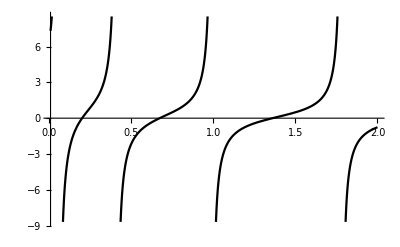

```mathematica
Plot[Rmat[Ε],{Ε,0.01,2.0}]
```

```mathematica
KK[Ε_]:=(f[0,√Ε,rmax]-dfdr[0,√Ε,rmax]Rmat[Ε])/(g[0,√Ε,rmax]-dgdr[0,√Ε,rmax]Rmat[Ε])
```

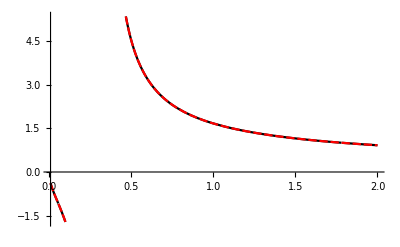

```mathematica
Plot[{KK[Ε],CalcCotanDelta[1,Ε,10]^-1},{Ε,0.01,2.0},PlotStyle->{Black,Red}]
```

Nails it!

Let’s see what this looks like for the case of no interaction.

- (∂^2 ψ(r))/(∂r^2)+(l(l+1))/r^2 ψ(r)=k^2 ψ(r)

For l=0 the solution is simply:

ψ(r)=A sin(k r)

Let’s see what the DVR solutions look like

```mathematica
W=DiagonalMatrix[wn];
T=Table[πfunsp[[i]].W.πfunsp[[j]],{i,2,M+2},{j,2,M+2}];
H=T;ValVecs=Sort[Transpose[Eigensystem[H]]];ProbSize=Length[ValVecs];
```

```mathematica
ValVecs[[1]]
```

{0.024674,{0.0000869861,0.00039074,0.000985175,0.00192595,0.0032574,0.00501521,0.00722765,0.00991623,0.013096,0.0167756,0.0209574,0.0256377,0.0308062,0.0364465,0.0425359,0.0490456,0.0559408,0.0631809,0.07072,0.0785073,0.0864874,0.094601,0.102786,0.110977,0.119109,0.127114,0.134926,0.14248,0.149712,0.156561,0.162972,0.168892,0.174274,0.179076,0.183265,0.18681,0.189688,0.191883,0.193385,0.194189,0.194294,0.193706,0.192432,0.190485,0.187875,0.184618,0.180726,0.176208,0.171072,0.165319,0.158942,0.151921,0.144222,0.135789,0.12653,0.116304,0.104884,0.0918779,0.07654,0.0570778,0.0229961}}

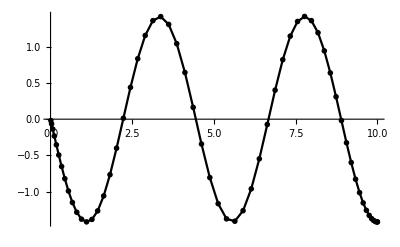

```mathematica
ntest=5;ListPlot[Table[{xn[[j]],ValVecs[[ntest,2,j-1]] πfuns[[j,j]]},{j,2,M+2}],Joined->True,PlotRange->All]
```

Note that all of these functions have vanishing derivative at the boundary.  That kinda makes sense since diagonalizing H̃ is tantamount to enforcing ((∂ψ)/(∂R))_b→0 by ignoring the surface term that arises from integration by parts.  So my first question is:

1) Why don’t we also get solutions for which ψ(b)→0 (which would lead to ψ^*(b)→0 also killing the surface term)?

2) How can one construct from these solutions (which have particular energy eigenvalues) the solution for a scattering wave function at a particular energy E?

3) Can we make clearer the connection between these solutions (which all have a common log-derivative of zero at R=b but different energies) and the solution at fixed energy E but nonzero log-derivative.

All of these questions are answered in the review by Lane and Thomas Rev. Mod. Phys. (1958) Section IV

```mathematica
Rmat[Ε_]:=Sum[(πfuns[[M+2,M+2]]ValVecs[[n,2,ProbSize]])^2/(ValVecs[[n,1]]-Ε),{n,1,ProbSize}];
```

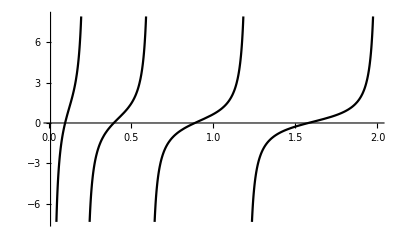

```mathematica
Plot[Rmat[ϵ]/rmax,{ϵ,0.01,2}]
```

```mathematica
Plot[(Sin[√ϵ rmax]/(√ϵ Cos[√ϵ rmax])),{ϵ,0.01,2}]
```

-Graphics-

Okay this seems to work!

### Lane and Thomas Section IV

a. The R function.

Consider two solutions to the Schrödinger equation:

(ⅆ^2 u_1(r))/(ⅆ r^2)+(2μ)/ℏ^2(E_1-V_eff(r))u_1=0

(ⅆ^2 u_2(r))/(ⅆ r^2)+(2μ)/ℏ^2(E_2-V_eff(r))u_2=0

Multiply the first of these equations by u_2 and the second by u_1, then integrate from zero to a, and subtract one from the other:

∫_0^a ⅆr((ⅆ^2 u_1(r))/(ⅆ r^2)u_2(r)-(ⅆ^2 u_2(r))/(ⅆ r^2)u_1(r)+(2μ)/ℏ^2(E_1-V_eff(r))u_1 u_2-(2μ)/ℏ^2(E_2-V_eff(r))u_1 u_2)=0

Terms with V_eff cancel.  Integration by parts of the first two terms gives:

-∫_0^a ⅆr ((ⅆu_1(r))/ⅆr(ⅆu_2(r))/ⅆr-(ⅆu_2(r))/ⅆr(ⅆu_1(r))/ⅆr)+((ⅆ u_1)/ⅆr u_2-u_1(ⅆ u_2)/ⅆr)_0^a+(2μ)/ℏ^2(E_1-E_2)∫_0^a ⅆr u_1 u_2=0

The first term clearly vanishes.  We arrive at a “Green’s theorem” for two solutions:

((ⅆ u_1)/ⅆr u_2-u_1(ⅆ u_2)/ⅆr)_0^a+(2μ)/ℏ^2(E_1-E_2)∫_0^a ⅆr u_1 u_2=0

More generally the region could be a box from r=a_l to r=a_r.

((ⅆ u_1)/ⅆr u_2-u_1(ⅆ u_2)/ⅆr)_a_l^a_r=(2μ)/ℏ^2(E_2-E_1)∫_a_l^a_r ⅆr u_1 u_2

((ⅆ u_1)/ⅆr u_2-u_1(ⅆ u_2)/ⅆr)_a_r=(2μ)/ℏ^2(E_2-E_1)∫_a_l^a_r ⅆr u_1 u_2

Usually (always when a_l=0), the lower limit vanishes since u(r)→0 at the origin. Now at particular energies E_λ,  the solutions u_λ have (ⅆu_λ(a))/ⅆr→0.  These are eigenstates satisfying u_λ(0)=0,(ⅆu_λ(a))/ⅆr→0.  The above equation then gives:

(2μ)/ℏ^2(E_2-E_1)∫_a_l^a_r ⅆr u_1 u_2=0

For non-degenerate states, this immediately gives the orthogonality relation:

∫_a_l^a_r ⅆr u_λ u_λ'=δ_λλ'

Now the solution u_E(r) for any energy can be expanded in the complete set of solutions u_λ:

u_E(r)=∑_λ A_λ u_λ(r)        0≤r≤ a

A_λ=∫_0^a u_E(r)u_λ(r)ⅆr

Using Green’s theorem again, with u_1=u_E and u_2=u_λ we see:

((ⅆ u_E)/ⅆr u_λ-u_E(ⅆ u_λ)/ⅆr)_a=(2μ)/ℏ^2(E_λ-E)∫_0^a ⅆr u_E u_λ

(ⅆu_E(a))/ⅆr u_λ(a)=(2μ)/ℏ^2(E_λ-E)∫_0^a ⅆr u_E u_λ

∫_0^a ⅆr u_E u_λ=A_λ=ℏ^2/(2μ)(u_λ(a))/(E_λ-E)(ⅆu_E(a))/ⅆr

Plugging this back into the expansion,

u_E(r)=(ⅆu_E(a))/ⅆr ∑_λ ℏ^2/(2μ)(u_λ(a)u_λ(r))/(E_λ-E)

(u_E(a)[(ⅆu_E(a))/ⅆr])^-1=∑_λ ℏ^2/(2μ)[u_λ(a)]^2/(E_λ-E)